```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\1d_tools.wl"]
```

```mathematica
ClearAll
```

```mathematica
ruleno = 50845; (*An interesting rule*)
nrods = 30;   (*Number of rods in the rod assembly*)
nupdates = 10000;  (*Number of updates for the CA*)
long = 1.5;  (*Length of rod when extended*)
short =0.5;  (*Length of rod when contracted*)
trail = RodEvolution[ruleno,nrods,nupdates]; (*Run the CA for given rule*)
rodstates = trail[[All,2;;-2]]; (*Remove the boundary conditions that do not have "physical" meaning*)
rodlengths = rodstates/.{1->long,0->short}; (*Replace 1/0 with long/short*)
totaltravel = Total[rodlengths,{2}]; (*The total length of the rod assembly at a cetain state*)
```

### How states evolve over time

```mathematica
ArrayPlot[rodstates[[;;20,All]]]
```

-Graphics-

#### What is the total length of the rod assembly as time progresses?

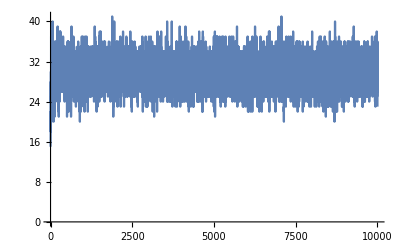

```mathematica
ListLinePlot[totaltravel,PlotRange->All]
```

```mathematica
Min[totaltravel]
```

50.

#### Are all possible total lengths covered given the current rule and number of evolutions?

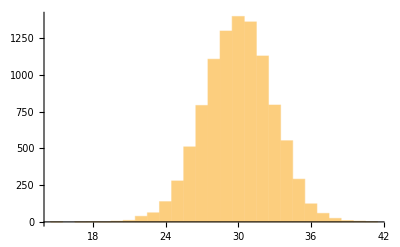

```mathematica
Histogram[totaltravel]
```

#### How does the rod assembly look at a certain state?

```mathematica
GraphRodAssembly[nupdatesmade_,rodlengths_,rodstates_]:={
staterodlengths = rodlengths[[nupdatesmade]];
staterodstartpoints = Prepend[Accumulate[staterodlengths],0] ;
staterodstate = rodstates[[nupdatesmade]];
rodgraphspecs = GraphSingleRod[staterodstartpoints[[#]],staterodstate[[#]]]&/@Range[Length[staterodstate]];
Show[Graphics[rodgraphspecs],Axes->{True,False},PlotRange->{{0,Max[totaltravel]},{0,2}}]
}
```

After 8194 updates, the rod should look like this:

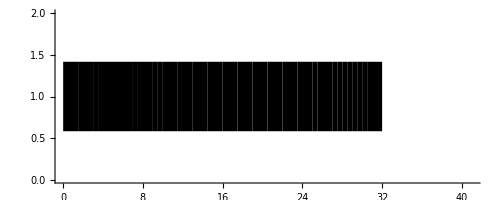

```mathematica
updatesmade = RandomInteger[nupdates];
Print["After ",updatesmade, " updates, the rod should look like this:"]
Show[GraphRodAssembly[updatesmade,rodlengths,rodstates]]
```

#### Go to state using a certain number of updates

```mathematica
Manipulate[Column[{updates,Show[GraphRodAssembly[updates,rodlengths,rodstates]]}],{updates,1,nupdates,1}]
```

Show::gtype: GraphRodAssembly is not a type of graphics.

```mathematica
|
```

#### n_updates required for a given total rod assembly travel

```mathematica
controlrules = KeySort[AssociationThread[Reverse@totaltravel->Reverse@Range[Length[totaltravel]]]] (*Distance to travel->Number of times to apply rule*)
```

<|15.→1,17.→2,18.→3,19.→4,20.→30,21.→5,22.→6,23.→577,24.→11,25.→14,26.→45,27.→9,28.→10,29.→16,30.→12,31.→26,32.→19,33.→34,34.→18,35.→28,36.→48,37.→17,38.→66,39.→216,40.→64,41.→1886|>

#### Number of updates required to reach a specified travel

```mathematica
Animate[Column[{controlrules[traveldistance],Show[GraphRodAssembly[controlrules[traveldistance],rodlengths,rodstates]]}],{traveldistance,Keys[controlrules]},AnimationRunning->False]
```